```mathematica
M1=3;M2=1;Q=4;
```

```mathematica
s={{0.1,0.1,0.9},{0.1,0.9,0.9},{0.9,0.1,0.9},{0.9,0.9,0.9}};
```

```mathematica
S=Exp[I 2 Pi s]; (*Eingabemuster*)
```

```mathematica
r={{0.1},{0.9},{0.9},{0.1}};
```

```mathematica
R=Exp[I 2 Pi r]; (*Ausgabemuster*)
```

```mathematica
X0=Table[Exp[I RandomInteger[{1,256}]/256.],{M1},{M2}];
```

```mathematica
(*Lernen auf der Testmenge:*)
```

```mathematica
X=X0;
```

```mathematica
Do[X=X+Outer[Times,Conjugate[S[[i]]],(R[[i]]-1/M1*S[[i]].X)],{i,1,Q}];
```

```mathematica
(*Zuordnung und Fehlerberechnung nach jeder Lernperiode:*)
```

```mathematica
STest=S[[1]];
```

```mathematica
rgoal=r[[1]];
```

```mathematica
X=X0;
```

```mathematica
TT=Table[Do[X=X+Outer[Times,Conjugate[S[[i]]],(R[[i]]-1/M1*S[[i]].X)],{i,1,Q}];
rneu=Mod[Arg[(1/M1 STest.X)]/(2 Pi),1];((rneu-rgoal).(rneu-rgoal))^0.5/M2,{100}];
```

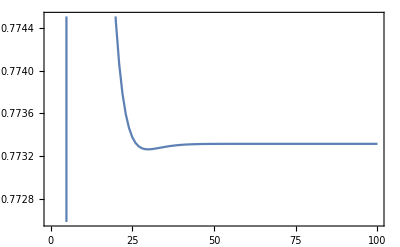

```mathematica
ListPlot[TT,Frame->True,Axes->None,Joined->True]
```

```mathematica
Mod[Arg[(1/M1 S[[4]].X)]/(2 Pi),1]
```

{0.1}